```mathematica
Clear["Global`*"]
SetDirectory[FileNameJoin[{NotebookDirectory[],"../figs/"}]]
```

/Users/marknovak/Git/aaaManuscripts/GeometricComplexity/GeometricComplexity/figs

SC_2= -Log_ef(x|(Θ̂)_x)+k/2 Log_e(n/(2 π))+Log_e∫_Θ √(det I(Θ))ⅆΘ + o(1);
The first term is the likelihood. The second term is the parameter and sample size dependent component.
The third term containing I(Θ), the Expected Fisher Information Matrix, reflects the model's flexibility.

```mathematica
cm=72/2.54;
```

### Second Term dependence on k and n

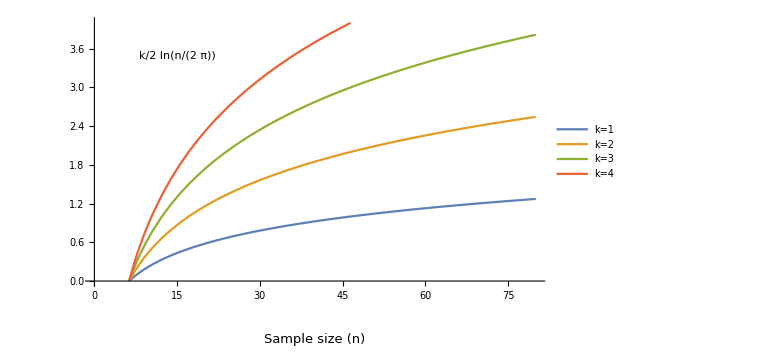

```mathematica
nmax=80;
p1=
Plot[
Evaluate@Table[k/2 Log[n/(2 π)],{k,1,4}],{n,1,nmax},
PlotRange->{{0,nmax},{0,4}},
PlotLegends->Placed[{"k=1","k=2","k=3", "k=4"},Above],
PlotRangeClipping->False,
ImagePadding->{{50,5}, {30, 5}},
Epilog->{
Style[Text["k/2"ln[n/(2 π)],{15,3.5}],12],
Text[Style["Sample size (n)",13],Scaled[{0.5,-0.2}]],Rotate[Text[Style["Parametric\ncomplexity",13],Scaled[{-0.2,0.5}]],90 Degree]
},
ImageSize->Large
]
Export["ParamComp_2ndTerm.pdf",Show[p1,ImageSize-> 8 cm]];
```

For reference, the sample size of the largest dataset in Novak & Stouffer 2021 is n = 528.
The smallest is n = 10.
And the median is n = 80.

```mathematica
PC=Round[
N[{Table[k/2 Log[n/(2 π)]/.n-> 10,{k,1,4}],
Table[k/2 Log[n/(2 π)]/.n-> 80,{k,1,4}],
Table[k/2 Log[n/(2 π)]/.n-> 528,{k,1,4}]}]
,1/10.]//Transpose//TableForm
```

0.2 | 1.3 | 2.2
0.5 | 2.5 | 4.4
0.7 | 3.8 | 6.6
0.9 | 5.1 | 8.9